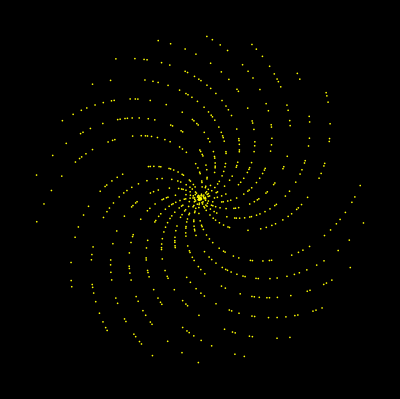

```mathematica
ListPolarPlot[{#,#}&/@Table[Prime[n],{n,666}],PlotStyle->{RGBColor[255,240,0],PointSize[0.003]},PlotTheme->"BlackBackground",ImageSize->Full,Axes->False]
```

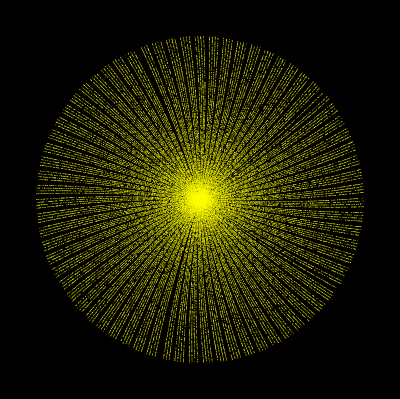

```mathematica
ListPolarPlot[{#,#}&/@Table[Prime[n],{n,66666}],PlotStyle->{RGBColor[255,240,0],PointSize[0.001]},PlotTheme->"BlackBackground",ImageSize->Full,Axes->False]
```

```mathematica
{#,#}&/@Table[Prime[n],{n,20}]
```

{{2,2},{3,3},{5,5},{7,7},{11,11},{13,13},{17,17},{19,19},{23,23},{29,29},{31,31},{37,37},{41,41},{43,43},{47,47},{53,53},{59,59},{61,61},{67,67},{71,71}}

```mathematica
Table[44n,{n,100}]
```

{44,88,132,176,220,264,308,352,396,440,484,528,572,616,660,704,748,792,836,880,924,968,1012,1056,1100,1144,1188,1232,1276,1320,1364,1408,1452,1496,1540,1584,1628,1672,1716,1760,1804,1848,1892,1936,1980,2024,2068,2112,2156,2200,2244,2288,2332,2376,2420,2464,2508,2552,2596,2640,2684,2728,2772,2816,2860,2904,2948,2992,3036,3080,3124,3168,3212,3256,3300,3344,3388,3432,3476,3520,3564,3608,3652,3696,3740,3784,3828,3872,3916,3960,4004,4048,4092,4136,4180,4224,4268,4312,4356,4400}

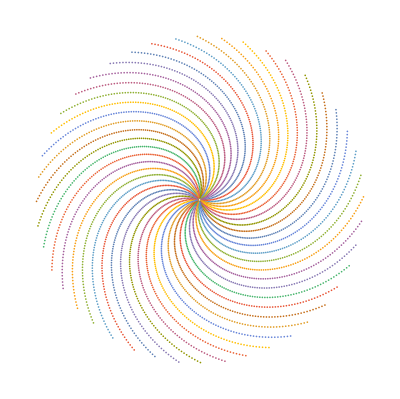

```mathematica
ListPolarPlot[Table[Table[{44n+k,44n+k},{n,113}],{k,0,43}],PlotStyle->PointSize[0.003],ImageSize->Full,Axes->False]
```

```mathematica
Table[Hue[fac/65],{fac,64}]
```

{Hue[Rational[1, 65]],Hue[Rational[2, 65]],Hue[Rational[3, 65]],Hue[Rational[4, 65]],Hue[Rational[1, 13]],Hue[Rational[6, 65]],Hue[Rational[7, 65]],Hue[Rational[8, 65]],Hue[Rational[9, 65]],Hue[Rational[2, 13]],Hue[Rational[11, 65]],Hue[Rational[12, 65]],Hue[Rational[1, 5]],Hue[Rational[14, 65]],Hue[Rational[3, 13]],Hue[Rational[16, 65]],Hue[Rational[17, 65]],Hue[Rational[18, 65]],Hue[Rational[19, 65]],Hue[Rational[4, 13]],Hue[Rational[21, 65]],Hue[Rational[22, 65]],Hue[Rational[23, 65]],Hue[Rational[24, 65]],Hue[Rational[5, 13]],Hue[Rational[2, 5]],Hue[Rational[27, 65]],Hue[Rational[28, 65]],Hue[Rational[29, 65]],Hue[Rational[6, 13]],Hue[Rational[31, 65]],Hue[Rational[32, 65]],Hue[Rational[33, 65]],Hue[Rational[34, 65]],Hue[Rational[7, 13]],Hue[Rational[36, 65]],Hue[Rational[37, 65]],Hue[Rational[38, 65]],Hue[Rational[3, 5]],Hue[Rational[8, 13]],Hue[Rational[41, 65]],Hue[Rational[42, 65]],Hue[Rational[43, 65]],Hue[Rational[44, 65]],Hue[Rational[9, 13]],Hue[Rational[46, 65]],Hue[Rational[47, 65]],Hue[Rational[48, 65]],Hue[Rational[49, 65]],Hue[Rational[10, 13]],Hue[Rational[51, 65]],Hue[Rational[4, 5]],Hue[Rational[53, 65]],Hue[Rational[54, 65]],Hue[Rational[11, 13]],Hue[Rational[56, 65]],Hue[Rational[57, 65]],Hue[Rational[58, 65]],Hue[Rational[59, 65]],Hue[Rational[12, 13]],Hue[Rational[61, 65]],Hue[Rational[62, 65]],Hue[Rational[63, 65]],Hue[Rational[64, 65]]}

```mathematica
ImageCollage[Table[ListPolarPlot[Table[Table[{fac n+k,fac n+k},{n,113}],{k,1}],PlotStyle->{Hue[fac/64],Thin},Axes->False,Joined->True],{fac,64}],Background->White]
```

-Graphics-

### Euler’s totient function

Euler’s totient function counts the positive integers up to a given integer n that are relatively prime to n. It is written using the Greek letter phi as φ(n) or ϕ(n), and may also be called Euler’s phi function. In other words, it is the number of integers k in the range 1 ≤ k ≤ n for which the greatest common divisor gcd(n, k) is equal to 1. The integers k of this form are sometimes referred to as totatives of n.

```mathematica
EulerPhi[44]
```

20

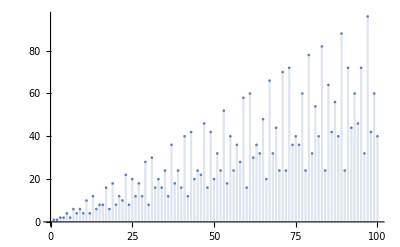

```mathematica
DiscretePlot[EulerPhi[k],{k,100}]
```

```mathematica
Partition[Table[EulerPhi[k],{k,100}],10]//Grid
```

1 | 1 | 2 | 2 | 4 | 2 | 6 | 4 | 6 | 4
10 | 4 | 12 | 6 | 8 | 8 | 16 | 6 | 18 | 8
12 | 10 | 22 | 8 | 20 | 12 | 18 | 12 | 28 | 8
30 | 16 | 20 | 16 | 24 | 12 | 36 | 18 | 24 | 16
40 | 12 | 42 | 20 | 24 | 22 | 46 | 16 | 42 | 20
32 | 24 | 52 | 18 | 40 | 24 | 36 | 28 | 58 | 16
60 | 30 | 36 | 32 | 48 | 20 | 66 | 32 | 44 | 24
70 | 24 | 72 | 36 | 40 | 36 | 60 | 24 | 78 | 32
54 | 40 | 82 | 24 | 64 | 42 | 56 | 40 | 88 | 24
72 | 44 | 60 | 46 | 72 | 32 | 96 | 42 | 60 | 40

### Dirichlet’s theorem

Dirichlet’s theorem, statement that there are infinitely many prime numbers contained in the collection of all numbers of the form n a + b, in which the constants a and b are integers that have no common divisors except the number 1 (in which case the pair are known as being relatively prime) and the variable n is any natural number (1, 2, 3, …).

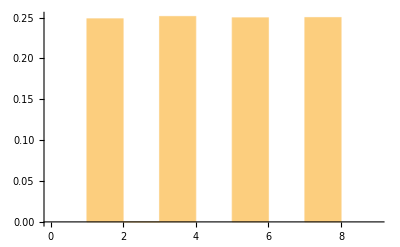

```mathematica
Histogram[Table[Mod[Prime[n],8],{n,10000}],{Range[0,9]},"Probability"]
```

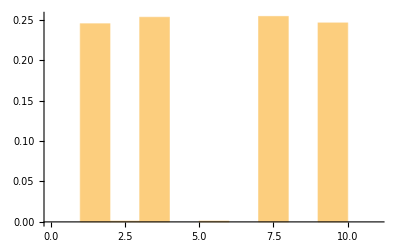

```mathematica
Histogram[Table[Mod[Prime[n],10],{n,1000}],{Range[0,11]},"Probability"]
```

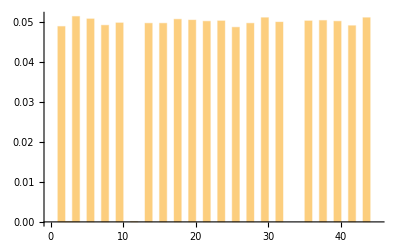

```mathematica
Histogram[Table[Mod[Prime[n],44],{n,10000}],{Range[0,45]},"Probability"]
```